```mathematica
J[x_,t_] = (((pr[x] - pl[x])#-1/(2N) D[((pr[x] + pl[x]) - (pr[x] - pl[x])^2) #,x]))&
```

(pr[x]-pl[x]) #1-(∂_x (((pr[x]+pl[x])-(pr[x]-pl[x])^2) #1))/(2 N)&

```mathematica
pr[x_] := 0.2+4x^4(1-x)
pl[x_] := 0.2 + 4x(1-x)^4
pde = Simplify[D[p[x,t],t] +D[J[x,t][p[x,t]],x]==0]
Δ= 0.0001
```

1/N((-4.+57. x-345. x^2+1160. x^3-2400. x^4+3192. x^5-2744. x^6+1440. x^7-360. x^8+N (0.5-4. x+9. x^2-10. x^3+5. x^4)) p[x,t]-0.125 N p^(0,1)[x,t]+0.5 p^(1,0)[x,t]-8. x p^(1,0)[x,t]+0.5 N x p^(1,0)[x,t]+57. x^2 p^(1,0)[x,t]-2. N x^2 p^(1,0)[x,t]-230. x^3 p^(1,0)[x,t]+3. N x^3 p^(1,0)[x,t]+580. x^4 p^(1,0)[x,t]-2.5 N x^4 p^(1,0)[x,t]-960. x^5 p^(1,0)[x,t]+1. N x^5 p^(1,0)[x,t]+1064. x^6 p^(1,0)[x,t]-784. x^7 p^(1,0)[x,t]+360. x^8 p^(1,0)[x,t]-80. x^9 p^(1,0)[x,t]+0.025 p^(2,0)[x,t]+0.25 x p^(2,0)[x,t]-2. x^2 p^(2,0)[x,t]+9.5 x^3 p^(2,0)[x,t]-28.75 x^4 p^(2,0)[x,t]+58. x^5 p^(2,0)[x,t]-80. x^6 p^(2,0)[x,t]+76. x^7 p^(2,0)[x,t]-49. x^8 p^(2,0)[x,t]+20. x^9 p^(2,0)[x,t]-4. x^10 p^(2,0)[x,t])==0

0.0001

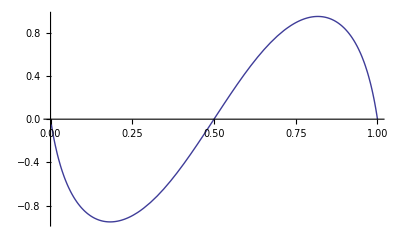

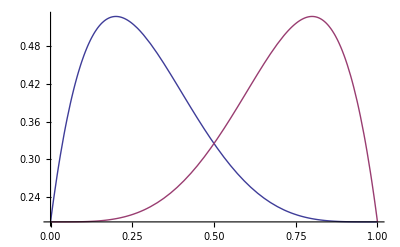

```mathematica
Plot[Log[pr[x]/pl[x]],{x,0,1}]
Plot[{pl[x],pr[x]},{x,0,1}]
```

```mathematica
DSolve[pde,p,{x,t}]
```

```mathematica
pinit[x] = 1/(2π 0.01^2)^0.5Exp[-(x-0.3)^2/(2 0.01^2)]
Integrate[pinit[x],{x,0,1}]
```

39.8942 ⅇ^(-5000. (-0.3+x)^2)

1.

```mathematica
nsol1 = NDSolve[{pde/.N->50,p[0 + Δ,t] == 0,p[1-Δ,t] ==0,p[x,0] == pinit[x]},p[x,t],{x,0+Δ,1-Δ},{t,0,2},AccuracyGoal->5]
```

{{p[x,t]→InterpolatingFunction[{{0.0001,0.9999},{0.,2.}},<>][x,t]}}

```mathematica
nsol1 = NDSolve[{pde,p[Δ,t] == p[1-Δ,t] ,p[x,0] == pinit[x]},p[x,t],{x,0+Δ,1-Δ},{t,0,1}]
```

{{p[x,t]→InterpolatingFunction[{{0.0001,0.9999},{0.,1.}},<>][x,t]}}

```mathematica
Plot3D[nsol1[[1,1,2]],{x,0 + Δ,1-Δ},{t,0,2}]
```

Plot3D::plln: Limiting value Δ in {x, 0 + Δ, 1 - Δ} is not a machine-sized real number.

Plot3D[nsol1⟦1,1,2⟧,{x,0+Δ,1-Δ},{t,0,2}]

```mathematica
Animate[Plot[nsol1[[1,1,2]]/.t->τ,{x,Δ,1-Δ},PlotRange->{0,2}],{τ,0.001,2}]
```

```mathematica
δ = 10Δ
```

0.001

```mathematica
pleft[τ_] := -NIntegrate[J[x,t][nsol1[[1,1,2]]]/.x -> δ,{t,0,τ}]
pright[τ_] :=NIntegrate[J[x,t][nsol1[[1,1,2]]]/.x -> (1-δ),{t,0,τ}]
pinside[τ_] :=NIntegrate[nsol1[[1,1,2]]/.t->τ,{x,δ,1-δ}]
```

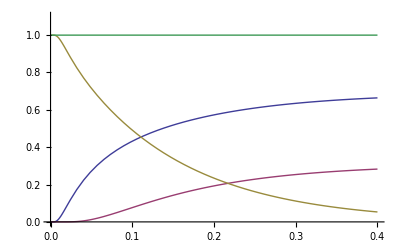

0.001

```mathematica
Plot[{pleft[t],pright[t],pinside[t],pleft[t] + pright[t] + pinside[t]},{t,0,0.4},PlotRange->{0,1.1}]
```

```mathematica
p0 = -NIntegrate[J[x,t][nsol1[[1,1,2]]]/.x -> δ,{t,0,0.4}]
p1 = NIntegrate[J[x,t][nsol1[[1,1,2]]]/.x -> (1-δ),{t,0,0.4}]
pint = NIntegrate[nsol1[[1,1,2]]/.t->0.4,{x,δ,1-δ}]
p0 + p1 + pint
```

NIntegrate::inumr: The integrand -0.003984023980008001` TagBox[« 1 », False, Rule[Editable, False]][0.001`, t] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 0.0000165036}}.

-NIntegrate[J[x,t][nsol1⟦1,1,2⟧]/.x→δ,{t,0,0.4}]

NIntegrate::inumr: The integrand 0.003984023980008004` TagBox[InterpolatingFunction[{{0.0001`, 0.9999`}, {0.`, 2.`}}, {4, 5, 1, {833, 134}, {6, 4}, 0, 0, 0, 0, Automatic}, « 1 », {Developer`PackedArrayForm, {0, 3, « 47 », 147, « 111573 »}, {1.989114756191945`*^-194, 1.8014398509481984`*^16, -1.989114756191945`*^-194, « 45 », 1.9881089174149693`*^-194, 1.8014398509481984`*^16, « 334816 »}}, {Automatic, Automatic}], False, Rule[Editable, False]][« 1 »] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.000530207, 0.000579072}}.

NIntegrate[J[x,t][nsol1⟦1,1,2⟧]/.x→1-δ,{t,0,0.4}]

0.831775

NIntegrate::inumr: The integrand -0.003984023980008001` TagBox[« 1 », False, Rule[Editable, False]][0.001`, t] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 0.0000165036}}.

NIntegrate::inumr: The integrand 0.003984023980008004` TagBox[InterpolatingFunction[{{0.0001`, 0.9999`}, {0.`, 2.`}}, {4, 5, 1, {833, 134}, {6, 4}, 0, 0, 0, 0, Automatic}, « 1 », {Developer`PackedArrayForm, {0, 3, « 47 », 147, « 111573 »}, {1.989114756191945`*^-194, 1.8014398509481984`*^16, -1.989114756191945`*^-194, « 45 », 1.9881089174149693`*^-194, 1.8014398509481984`*^16, « 334816 »}}, {Automatic, Automatic}], False, Rule[Editable, False]][« 1 »] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.000530207, 0.000579072}}.

0.831775+NIntegrate[J[x,t][nsol1⟦1,1,2⟧]/.x→1-δ,{t,0,0.4}]-NIntegrate[J[x,t][nsol1⟦1,1,2⟧]/.x→δ,{t,0,0.4}]

```mathematica
pr[x_] := 1.05x(1-x)
pl[x_] := 0.95x(1-x)
a[x_] := pr[x] - pl[x]
b[x_] :=(1/N)((pr[x] + pl[x]) - (pr[x] - pl[x])^2)
J[x_,t_] := ((a[x]#-1/2 D[b[x] #,x]))&
ψ[p_,n_] := Exp[-2 NIntegrate[a[x]/b[x]/.N->n,{x,0,p}]]
P1[p_,n_] := NIntegrate[ψ[y,n],{y,0,p}]/NIntegrate[ψ[y,n],{y,0,1}]
PlotPfix[n_] :=
Module[{Δ,δ,x0,Tend,σ},
     pde = Simplify[D[p[x,t],t] +D[J[x,t][p[x,t]],x]==0];
	Δ= 0.0001;
	δ = 10Δ;
	x0 = 1/n;
	Tend = 5;
	σ =(0.005);
	pinit[x] = 1/(2π σ^2)^0.5Exp[-(x-(1/n))^2/(2 σ^2)];
	nsol1 = NDSolve[{pde/.N->n,p[0 + Δ,t] == 0,p[1-Δ,t] ==0,p[x,0] == pinit[x]},p[x,t],{x,0+Δ,1-Δ},{t,0,Tend},AccuracyGoal->5];
	Plot3D[nsol1[[1,1,2]],{x,0 + Δ,1-Δ},{t,0,2}]
	(*{p1num = NIntegrate[J[x,t][nsol1[[1,1,2]]]/.{x -> (1-δ),N->n},{t,0,Tend}]};*)(*P1[x0]/.N->n*)]
```

```mathematica
PlotPfix[4]
```

NDSolve::eerr: Warning: scaled local spatial error estimate of 99.8113 at t = 5. in the direction of independent variable x is much greater than the prescribed error tolerance. Grid spacing with 1765 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

-Graphics3D-

NIntegrate::nlim: x = y is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

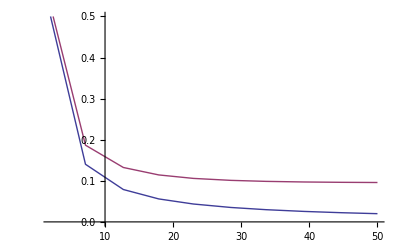

```mathematica
Plot[{1/x,P1[1/x,x]},{x,2,50},PlotPoints->10, MaxRecursion->0,PlotRange->{0,0.5}]
```